```mathematica
ClearAll["Global`*"];
NotebookDirectory[];
SetDirectory[NotebookDirectory[]]; (* or else the default directory is Directory[]*)
NotebookDirectory[];
```

# Active SSH

### Parameters

```mathematica
Mms=5.5*^-4*0.5;
Rms=0.34*0.09;
Cmc=1.750252936794995*^-4/0.42 ; (*490*^-6*1.5;*)
omega0 = 1/Sqrt[Mms*Cmc];


Sd=12*^-4;(* m^2 diaphragm surface *)
S=0.05*0.05; (*  m^2 duct cross section*)
rho0=1.184;(*[kg/m^3]*)
c0=346;(*%[m/s]*)
a=0.2806;(*[m]*)
pp =1/2;
pm =1/2;
thop =-0.5; (*0,*)
delta =a/4*thop

1/(2*Pi*Sqrt[Mms*Cmc])
```

-0.035075 Null

470.141

### Pressure Wave

```mathematica
p[k_,x_]:=pp*Exp[-I*(k*x)]+pm*Exp[+I*(k*x)];
(*Norm[p[k,0]]*)
```

### Speaker mechanical impedance

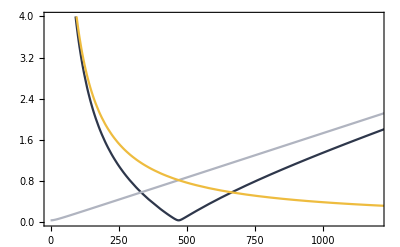

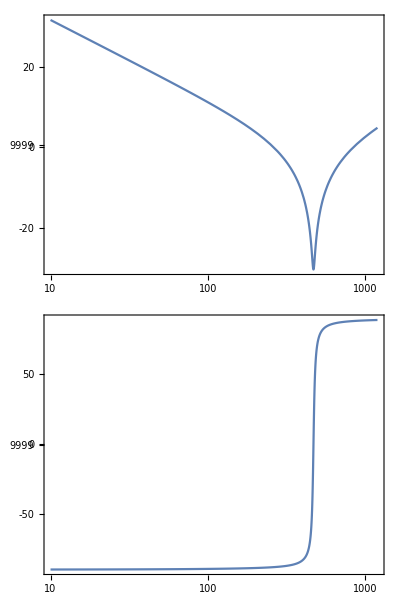

```mathematica
Zms[freq_]:= (I*2*Pi*freq)*Mms + Rms + 1/((I*2*Pi*freq)*Cmc);
ZmsAbv[freq_]:= (I*2*Pi*freq)*Mms + Rms ;
ZmsBlw[freq_]:=  Rms + 1/((I*2*Pi*freq)*Cmc);

Plot[{Abs[Zms[freq] ] ,Abs[ZmsAbv[freq]] ,Abs[ZmsBlw[freq] ]},{freq,0.1,2200},PlotRange->{{0,1200},{0,4}},PlotStyle->{ColorData["GrayYellowTones",0],ColorData["GrayYellowTones",0.5],ColorData["GrayYellowTones",1]},Frame->True]
BodePlot[Zms[f],{f,10,1200}]
```

### w parameter

The pressure is estimated with two microphones at centre (x = 0) and far edge (x = \pm a/2)

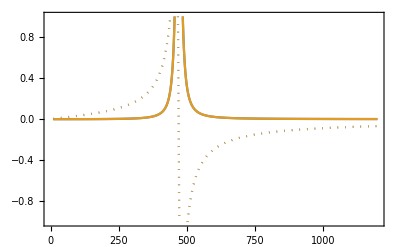

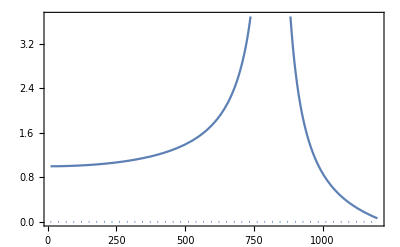

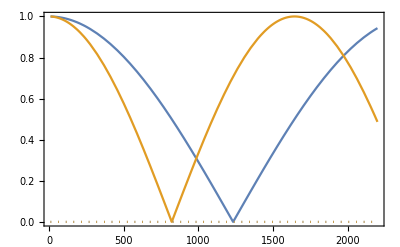

```mathematica
W[k_] := (c0*rho0/(2*S))*(Sd^2/Zms[c0*k/(2*Pi)]);
(*ReImPlot[W[2*Pi*freq/c0],{freq,10,1200},PlotRange->{{0,1200},{-0.01,0.01}},Frame->True]*)

(*wm[k_] := W [c0*k/(2*Pi)]/((Sin[k*(a/4-delta)]+Sin[k*delta]*Norm[p[k,0]]/Norm[p[k,a/4]])/Sin[k*a/4])
wp[k_] := W [c0*k/(2*Pi)]/((Sin[k*(-a/4+delta)]+Sin[-k*delta]*Norm[p[k,0]]/Norm[p[k,a/4]])/Sin[-k*a/4])*)


(*PressureEstimate[pos_]:=((Norm[p[k,a/4]]*(Sin[k*(a/2-(delta+a/4))]*Norm[p[k,a/2]]+Sin[k*(delta+a/4)]*Norm[p[k,0]]))/Sin[k*a/2])*)
wm[k_] :=W [k]+0*(Norm[p[k,-a/4]]/Norm[p[k,-a/4+delta]])
wp[k_] :=W [k]+0*(Norm[p[k,+a/4]]/Norm[p[k,+a/4-delta]])

(*ReImPlot[Norm[p[2*Pi*freq/c0,0]]/Norm[p[2*Pi*freq/c0,a/4]],{freq,0,1200}]*)


ReImPlot[{wm[2*Pi*freq/c0],wp[2*Pi*freq/c0]},{freq,10,1200},PlotRange->{{0,1200},{-1,1}},Frame->True]
ReImPlot[(Norm[p[2*Pi*freq/c0,+a/4]]/Norm[p[2*Pi*freq/c0,+a/4-delta]]),{freq,10,1200},Frame->True]
ReImPlot[{Norm[p[2*Pi*freq/c0,+a/4]],Norm[p[2*Pi*freq/c0,+a/4-delta]]},{freq,10,2200},Frame->True]
```

### Transfer Matrix

True system vs Virtual system

```mathematica
T1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});

T2m[k_]:= Inverse[({{(1+wm[k]*Exp[-I k delta]), +wm[k]*Exp[+I k delta]}, {-wm[k]*Exp[-I k delta], (1-wm[k]*Exp[+I k delta])}})];

T2p[k_]:= Inverse[({{(1+wp[k]*Exp[+I k delta]), +wp[k]*Exp[-I k delta]}, {-wp[k]*Exp[+I k delta], (1-wp[k]*Exp[-I k delta])}})];


(*T2m[k_]:= ({{(1-wm[k])*Exp[+I k delta], -wm[k]*Exp[+I k delta]}, {+wm[k]*Exp[-I k delta], (1+wm[k])*Exp[-I k delta]}});

T2p[k_]:= ({{(1-wp[k])*Exp[-I k delta], -wp[k]*Exp[-I k delta]}, {+wp[k]*Exp[+I k delta], (1+wp[k])*Exp[+I k delta]}});*)
T1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});

T2m[k_]:= Inverse[({{(1+wm[k]*Exp[-I k delta]), +wm[k]*Exp[+I k delta]}, {-wm[k]*Exp[-I k delta], (1-wm[k]*Exp[+I k delta])}})];

T2p[k_]:= Inverse[({{(1+wp[k]*Exp[+I k delta]), +wp[k]*Exp[-I k delta]}, {-wp[k]*Exp[+I k delta], (1-wp[k]*Exp[-I k delta])}})];

(*T1[k_] := ({{Exp[-I k *(a/4-delta)], 0}, {0, Exp[+I k*( a/4-delta)]}});

T2[k_]:= ({{(1-wm[k]), -wm[k]}, {+wm[k], (1+wm[k])}});
T3[k_] := ({{Exp[-I k *(a/4-delta)], 0}, {0, Exp[+I k*( a/4-delta)]}});

Ttot[k_]= T1[k].T2[k].T3[k].T3[k].T2[k].T1[k];*)
Ttot[k_]= T1[k].T2m[k].T1[k].T1[k].T2p[k].T1[k];

M11[k_]:= Part[Ttot[k],1,1];
M12[k_]:= Part[Ttot[k],1,2];
M21[k_]:= Part[Ttot[k],2,1];
M22[k_]:= Part[Ttot[k],2,2];



(* ORIGINAL MODEL
M11[k_]:= (1-wm[k])^2*Exp[-I*k*a] - wm[k]^2*Exp[+I*k*2*delta];
M12[k_]:=-wm[k]*((1-wm[k])*Exp[-I*k*a/2]+(1+wm[k])*Exp[+I*k*a/2]); (*WRONG?*)
M21[k_]:=-M12[k];
M22[k_]:= (1+wm[k])^2*Exp[+I*k*a] - wm[k]^2*Exp[-I*k*2*delta];
*)

(*
M11[k_]:= (1-W[k])^2*Exp[-I*k*a] - W[k]^2*Exp[+I*k*2*delta];
M12[k_]:=-W[k]*((1-W[k])*Exp[-I*k*a/2]+(1+W[k])*Exp[+I*k*a/2]*Exp[+I*k*2*delta]); 
M21[k_]:=W[k]*((1-W[k])*Exp[-I*k*a/2]*Exp[-I*k*2*delta]+(1+W[k])*Exp[+I*k*a/2]);
M22[k_]:= (1+W[k])^2*Exp[+I*k*a] - W[k]^2*Exp[-I*k*2*delta];
*)

(*
M11[k_]:= 4*((1-W[k])^2*Exp[-I*k*a]/(2*(1+Cos[k*delta])) - W[k]^2/(1+Exp[-I*k*2*delta])^2);
M12[k_]:=-W[k]*((1-W[k])*Exp[-I*k*a/2]+(1+W[k])*Exp[+I*k*a/2]*Exp[+I*k*2*delta]); 
M21[k_]:=W[k]*((1-W[k])*Exp[-I*k*a/2]*Exp[-I*k*2*delta]+(1+W[k])*Exp[+I*k*a/2]);
M22[k_]:= 4*((1+W[k])^2*Exp[+I*k*a]/(2*(1+Cos[k*delta])) - W[k]^2/(1+Exp[+I*k*2*delta])^2);
*)
(*
M11[k_]:= (1-wm[k])*(1-wp[k])*Exp[-I*k*a] - wm[k]*wp[k]*Exp[+I*k*2*delta];
M12[k_]:=-wp[k]*(1-wm[k])*Exp[-I*k*a/2]-wm[k]*(1+wp[k])*Exp[+I*k*a/2]*Exp[+I*k*2*delta]; 
M21[k_]:=+wm[k]*(1-wp[k])*Exp[-I*k*a/2]*Exp[-I*k*2*delta]+wp[k]*(1+wm[k])*Exp[+I*k*a/2];
M22[k_]:= (1+wm[k])*(1+wp[k])*Exp[+I*k*a] - wm[k]* wp[k]*Exp[-I*k*2*delta];
*)
(*
M11[k_]:= 1/4*(((1-2*W[k])^2 +2*(1-2*W[k])*Cos[k*delta]+1)*Exp[-I*k*a]  + ((1-2*W[k])*Exp[+I*k*delta]-1)*((1+2*W[k])*Exp[+I*k*delta]-1));
M12[k_]:=-W[k]*((1-W[k])*Exp[-I*k*a/2]+(1+W[k])*Exp[+I*k*a/2]*Exp[+I*k*2*delta]); (*WRONG*)
M21[k_]:=W[k]*((1-W[k])*Exp[-I*k*a/2]*Exp[-I*k*2*delta]+(1+W[k])*Exp[+I*k*a/2]); (*WRONG*)
M22[k_]:= 1/4*(((1+2*W[k])^2 +2*(1+2*W[k])*Cos[k*delta]+1)*Exp[+I*k*a]  + ((1+2*W[k])*Exp[-I*k*delta]-1)*((1-2*W[k])*Exp[-I*k*delta]-1));
*)
(*
M11[k_]:= (1-wm[k])*(1-wp[k])*Exp[-I*k*a] - wm[k]*wp[k]*Exp[+I*k*2*delta];
M12[k_]:=-wp[k]*(1-wm[k])*Exp[-I*k*a/2]-wm[k]*(1+wp[k])*Exp[+I*k*a/2]; (*WRONG?*)
M21[k_]:=+wm[k]*(1-wp[k])*Exp[-I*k*a/2]+wp[k]*(1+wm[k])*Exp[+I*k*a/2];(*WRONG?*)
M22[k_]:= (1+wm[k])*(1+wp[k])*Exp[+I*k*a] - wm[k]* wp[k]*Exp[-I*k*2*delta];
*)

(*
M11[k_]:= (1-wm[k])*(1-wp[k])*Exp[-I*k*a] - wm[k]*wp[k];
M12[k_]:=-wp[k]*(1-wm[k])*Exp[-I*k*a/4]-wm[k]*(1+wp[k])*Exp[+I*k*a/4]; (*WRONG?*)
M21[k_]:=+wm[k]*(1-wp[k])*Exp[-I*k*a/4]+wp[k]*(1+wm[k])*Exp[+I*k*a/4];(*WRONG?*)
M22[k_]:= (1+wm[k])*(1+wp[k])*Exp[+I*k*a] - wm[k]* wp[k];
*)


M[k_]:= {{M11[k],M12[k]},{M21[k],M22[k]}} ;
(*ReImPlot[M[2*Pi*freq/c0].M[2*Pi*freq/c0],{freq,10,1200},PlotRange->{{0,1200},{-1,1}},Frame->True]*)
MatrixForm[M[k]]//FullSimplify;
```

{{ⅇ^((0.-0.07015 ⅈ) k) (((0.+ⅇ^((0.-0.07015 ⅈ) k) (0.+ⅇ^((0.-0.07015 ⅈ) k) (0.+(ⅇ^((0.-0.07015 ⅈ) k) (1-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))))) (1-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))-(0.01392 ⅇ^((0.-6.93889×10^-18 ⅈ) k))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) ((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)^2)),ⅇ^((0.+0.07015 ⅈ) k) (-(0.117983 ⅇ^((0.+0.035075 ⅈ) k) (0.+ⅇ^((0.-0.07015 ⅈ) k) (0.+ⅇ^((0.-0.07015 ⅈ) k) (0.+(ⅇ^((0.-0.07015 ⅈ) k) (1-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))))))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))-(0.117983 ⅇ^((0.+0.035075 ⅈ) k) (1+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) ((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))},{ⅇ^((0.-0.07015 ⅈ) k) ((0.117983 ⅇ^((0.-0.035075 ⅈ) k) (0.+ⅇ^((0.+0.07015 ⅈ) k) (0.+ⅇ^((0.+0.07015 ⅈ) k) (0.+(ⅇ^((0.+0.07015 ⅈ) k) (1+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))))))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))+(0.117983 ⅇ^((0.-0.035075 ⅈ) k) (1-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) ((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))),ⅇ^((0.+0.07015 ⅈ) k) (((0.+ⅇ^((0.+0.07015 ⅈ) k) (0.+ⅇ^((0.+0.07015 ⅈ) k) (0.+(ⅇ^((0.+0.07015 ⅈ) k) (1+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))))) (1+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)))/((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k))-(0.01392 ⅇ^((0.+6.93889×10^-18 ⅈ) k))/(((1.+0. ⅈ)+(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)-(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) ((1.+0. ⅈ)-(0.117983 ⅇ^((0.-0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)+(0.117983 ⅇ^((0.+0.035075 ⅈ) k))/(0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)) (0.0306-(0.+6.93541 ⅈ)/k+(0.+0.09515 ⅈ) k)^2))}}

### Scattering Matrix

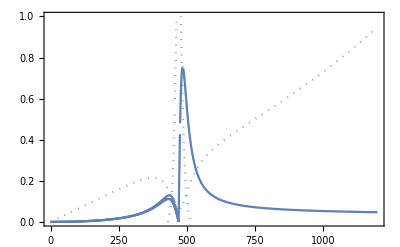

```mathematica
SS[k_]:= {{-M21[k]/M22[k],1/M22[k]},{M11[k]-M12[k]*M21[k]/M22[k],M12[k]/M22[k]}};

SSm[k_]:= {{-Part[T2m[k],2,1]/Part[T2m[k],2,2],1/Part[T2m[k],2,2]},{Part[T2m[k],1,1]-Part[T2m[k],1,2]*Part[T2m[k],2,1]/Part[T2m[k],2,2],Part[T2m[k],1,2]/Part[T2m[k],2,2]}};
SSp[k_]:= {{-Part[T2p[k],2,1]/Part[T2p[k],2,2],1/Part[T2p[k],2,2]},{Part[T2p[k],1,1]-Part[T2p[k],1,2]*Part[T2p[k],2,1]/Part[T2p[k],2,2],Part[T2p[k],1,2]/Part[T2p[k],2,2]}};


MatrixForm[SSm[k]]//FullSimplify;
MatrixForm[SSp[k]]//FullSimplify;

ReImPlot[(SSm[2*Pi*freq/c0]-SSp[2*Pi*freq/c0])/(SSm[2*Pi*freq/c0]+SSp[2*Pi*freq/c0]),{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True]
```

### Dispersion

3.56379 ArcCos[(0.5 ⅇ^((0.+0.2806 ⅈ) k) k^2+0.5 ⅇ^((0.+0.4209 ⅈ) k) k^2+ⅇ^((0.+0.035075 ⅈ) k) k ((0.-29.3915 ⅈ)+(0.129679+(0.+0.403235 ⅈ) k) k)+ⅇ^((0.+0.105225 ⅈ) k) k ((0.-29.3915 ⅈ)+(0.129679+(0.+0.403235 ⅈ) k) k)+ⅇ^((0.+0.596275 ⅈ) k) k ((-8.10463×10^-15+29.3915 ⅈ)+((-0.129679+4.44089×10^-16 ⅈ)+(1.38778×10^-16-0.403235 ⅈ) k) k)+ⅇ^((0.+0.666425 ⅈ) k) k ((-8.10463×10^-15+29.3915 ⅈ)+((-0.129679+4.44089×10^-16 ⅈ)+(1.38778×10^-16-0.403235 ⅈ) k) k)+ⅇ^((0.+0.07015 ⅈ) k) (1727.72+k ((0.+15.2459 ⅈ)+k (-47.9404+((0.-0.209165 ⅈ)+0.325197 k) k)))+ⅇ^((0.+0.63135 ⅈ) k) ((1727.72-7.10543×10^-15 ⅈ)+k ((2.84217×10^-14+15.2459 ⅈ)+k ((-47.9404-3.33067×10^-16 ⅈ)+((4.44089×10^-16-0.209165 ⅈ)+0.325197 k) k))))/(1. ⅇ^((0.+0.2806 ⅈ) k) k^2+1. ⅇ^((0.+0.4209 ⅈ) k) k^2+ⅇ^((0.+0.35075 ⅈ) k) (3455.45+k ((0.+30.4918 ⅈ)+k (-96.8809+((0.-0.418331 ⅈ)+0.650395 k) k))))]

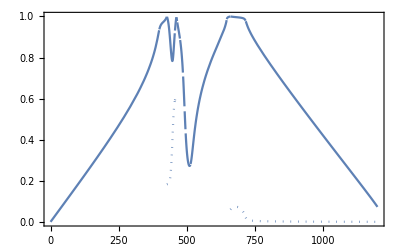

```mathematica
TrFunc[k_]:= Tr[M[k]]/2 ;
(*TrFunc[k_]:= Tr[M[k]]- Sqrt[Tr[M[k]]^2-4*Det[Tr[M[k]]]];*)
(*TraceM1[k_]:= (M11[k]+ M22[k])/2- Sqrt[((M11[k]+ M22[k])/2)^2+M12[k]+ M21[k]];*)

q[k_] :=ArcCos[ TrFunc[k]]/a;
q[k]//FullSimplify
FullSimplify[%];
ToMatlab[%];
ReImPlot[q[2*Pi*freq/c0]*a/Pi,{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True]
```

### Energy conserving = S-matrix is unitary

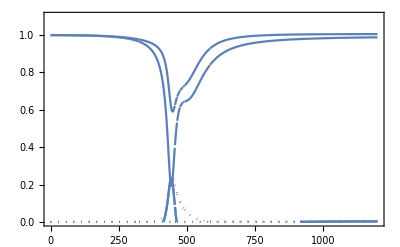

```mathematica
ReImPlot[SS[2*Pi*freq/c0].Transpose[Conjugate[SS[2*Pi*freq/c0]]],{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]
```

### SU (1, 1) group?

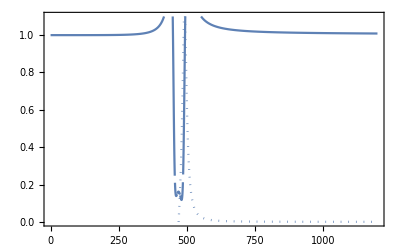

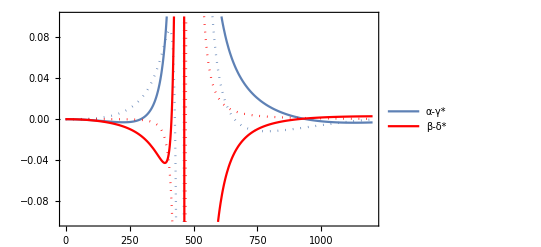

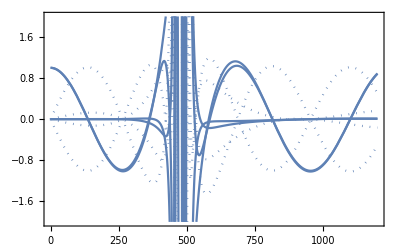

```mathematica
ReImPlot[M11[2*Pi*freq/c0]*M22[2*Pi*freq/c0] - M12[2*Pi*freq/c0]*M21[2*Pi*freq/c0] ,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]
p1 = ReImPlot[M11[2*Pi*freq/c0]-Conjugate[M22[2*Pi*freq/c0]]  ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"α-γ*"}]];
p2 = ReImPlot[M12[2*Pi*freq/c0]-Conjugate[M21[2*Pi*freq/c0]]  ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"β-δ*"}],PlotStyle->Red];
Show[p1,p2, PlotRange->All]

ReImPlot[MatrixPower[M[2*Pi*freq/c0],2],{freq,0.1,1200},PlotRange->{{0,1200},{-2,2}},Frame->True]
```

### Topology

```mathematica
AlphaR[k_]:= Re[M11[k]]
AlphaI[k_]:=Im[M11[k]]
BetaR[k_]:=Re[M21[k]]
BetaI[k_]:=Im[M21[k]]

coneplot = Plot3D[{Sqrt[x^2+y^2],-Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,
ColorFunction->"RustTones",
PlotStyle->Opacity[0.5],
Mesh-> False,
Boxed->False,
Axes->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[1],
TicksStyle->None,
AxesLabel->{Style[hi,16],Style[y,16],Style[z,16]},
ViewPoint->{Pi,Pi/2,2},Background->None]
Export["cone.png",coneplot,Background->None,ImageResolution-> 300]

Directory[]
```

-Graphics3D-

cone.png

C:\Users\padlewsk\Documents (Local)\projects\SSH\mathematica\AA2

### Mapping to spring/mass model

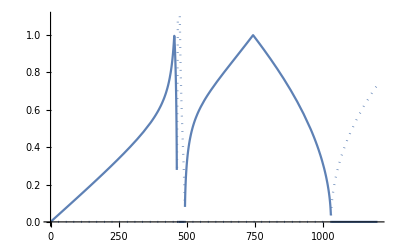

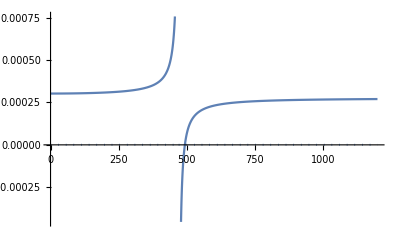

```mathematica
k1 =2800;
k2 =2800;


Meff[omega_]:= Mms*( 1+0.1*omega0^2/(omega0^2-omega^2));
q2[omega_]:=ArcCos[1-(Meff[omega]*omega^2)*(2*k1 + 2*k2 - (Meff[omega]*omega^2))/(2*k1*k2)]/a;
FullSimplify[%]
q2[omega];
ReImPlot[q2[omega]*a/Pi,{omega,0,1000}];
ReImPlot[q2[2*Pi*freq]*a/Pi,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}}]
ReImPlot[Meff[2*Pi*freq],{freq,0,1200}]
FullSimplify[%];
```

### Test...

```mathematica
f[x_]:= Exp[I*2*Pi*freq/c0*a/8]
```

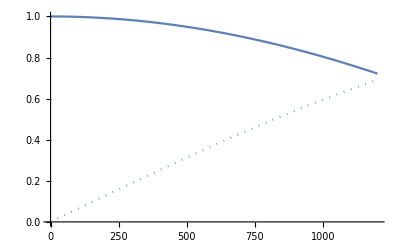

```mathematica
ReImPlot[f[freq],{freq,0,1200}]
```